```mathematica
p1[x_]:= a1*x^3+b1*x^2+c1*x+d1
p2[x_] := a2*x^3+b2*x^2+c2*x+d2
p3[x_] := 0.5
p4[x_] := a4*x^3+b4*x^2+c4*x+d4
p5[x_] :=0.07*x - 0.76
p6[x_] := a6*x^3+b6*x^2+c6*x+d6
p7[x_]:=0.00777778x+0.98222216
```

```mathematica
(1.2-.5)/(28-18)
(1.305 - 1.2)/(41.5-28)
```

0.07

0.00777778

```mathematica
Solve[{p1[0]==0.5,p1[3/8]==1, p1[3/4]==0.5,p1'[3/8]==0},{a1,b1,c1,d1}]
```

{{a1→0.,b1→-3.55556,c1→2.66667,d1→0.5}}

```mathematica
{a1,b1,c1,d1}/.{{a1->0.,b1->-3.5555555555555554,c1->2.6666666666666665,d1->0.5}}
```

{{0.,-3.55556,2.66667,0.5}}

```mathematica
p1[x_] := -3.55556*x^2 + 2.66667*x + 0.5
```

```mathematica
p1[x]
```

0.5+2.66667 x-3.55556 x^2

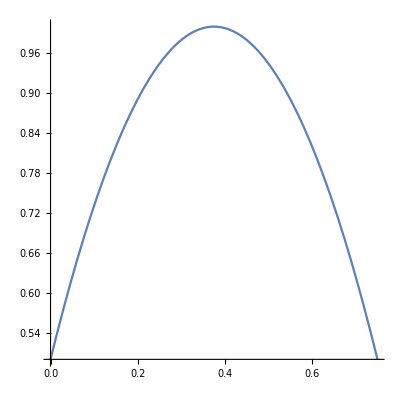

```mathematica
Plot[p1[x], {x, 0, 0.75}, AspectRatio->1]
```

```mathematica
spline[x_]:= Piecewise[{{p1[x], 0≤ x≤ 0.75},{p3[x],0.75<x≤ 18},{p5[x],18<x≤28},{p7[x],28<x≤41.5}}]
```

```mathematica
spline[0.75]
```

0.5

```mathematica
p5[28]
```

1.2

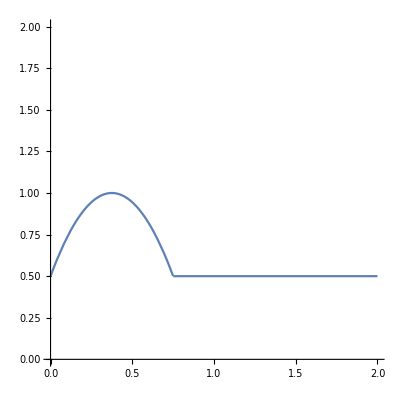

```mathematica
Plot[spline[x],{x,0,2}, AspectRatio->1, PlotRange->{0,2}]
```

```mathematica
f = Interpolation[{{0,0.5},{3/8,1},{3/4,0.5},{1,0.5},{2,0.5},{18,0.5},{28,1.2},{41.5,1.3}}]
```

InterpolatingFunction[…]

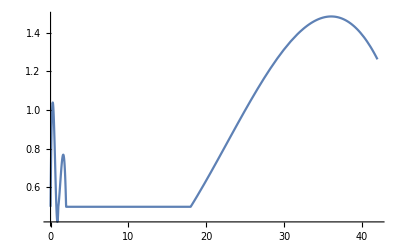

```mathematica
Plot[f[x],{x,0,42}]
```